### Dirac Basis

#### Matrices definition

```mathematica
σ= {{{1,0},{0,1}},{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
σto={{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}},{{0, 0, -I, 0}, {0, 0, 0, -I}, {I, 0, 0, 0}, {0, I, 0, 0}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}}};

otτ={{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}},{{0, -I, 0, 0}, {I, 0, 0, 0}, {0, 0, 0, -I}, {0, 0, I, 0}},{{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}};
τ = {ArrayFlatten[{{otτ[[1]],0},{0,otτ[[1]]}}],ArrayFlatten[{{otτ[[2]],0},{0,otτ[[2]]}}],ArrayFlatten[{{otτ[[3]],0},{0,otτ[[3]]}}],ArrayFlatten[{{otτ[[4]],0},{0,otτ[[4]]}}]};
{τ[[1]]//MatrixForm,τ[[2]]//MatrixForm,τ[[3]]//MatrixForm,τ[[4]]//MatrixForm};
γD = {ArrayFlatten[{{σto[[1]],0},{0,-σto[[1]]}}],ArrayFlatten[{{0,σto[[2]]},{-σto[[2]],0}}],ArrayFlatten[{{0,σto[[3]]},{-σto[[3]],0}}],ArrayFlatten[{{0,σto[[4]]},{-σto[[4]],0}}]};
{γD[[1]]//MatrixForm,γD[[2]]//MatrixForm,γD[[3]]//MatrixForm,γD[[4]]//MatrixForm};
```

#### Finding Eigenvalues[] and EigenVectors[]

```mathematica
DiracHamiltonianD=-M[t]*γD[[1]]-γD[[1]].γD[[4]]*k+f[t]/2(Sum[γD[[1]].γD[[i]].τ[[i]],{i,2,4}]);
AnsD=FullSimplify[Eigensystem[-M[t]*γD[[1]]-γD[[1]].γD[[4]]*k+f[t]/2(Sum[γD[[1]].γD[[i]].τ[[i]],{i,2,4}])]];
```

```mathematica
ωD = Table[AnsD[[1]][[i]],{i,1,8}]
uD = Table[AnsD[[2]][[i]],{i,1,8}]
```

{-1/2 √((-2 k+f[t])^2+4 M[t]^2),1/2 √((-2 k+f[t])^2+4 M[t]^2),-1/2 √((2 k+f[t])^2+4 M[t]^2),1/2 √((2 k+f[t])^2+4 M[t]^2),-1/2 √(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2)),1/2 √(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2)),-1/2 √(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2)),1/2 √(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2))}

{{(2 M[t]+√((-2 k+f[t])^2+4 M[t]^2))/(2 k-f[t]),0,0,0,1,0,0,0},{(2 M[t]-√((-2 k+f[t])^2+4 M[t]^2))/(2 k-f[t]),0,0,0,1,0,0,0},{0,0,0,-(2 M[t]+√((2 k+f[t])^2+4 M[t]^2))/(2 k+f[t]),0,0,0,1},{0,0,0,(-2 M[t]+√((2 k+f[t])^2+4 M[t]^2))/(2 k+f[t]),0,0,0,1},{0,((-k f[t]+√(f[t]^2 (k^2+f[t]^2))) (2 M[t]+√(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))))/(f[t]^3-2 f[t] √(f[t]^2 (k^2+f[t]^2))),(f[t] (2 M[t]+√(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))))/(f[t]^2-2 √(f[t]^2 (k^2+f[t]^2))),0,0,(-k f[t]+√(f[t]^2 (k^2+f[t]^2)))/f[t]^2,1,0},{0,((k f[t]-√(f[t]^2 (k^2+f[t]^2))) (-2 M[t]+√(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))))/(f[t]^3-2 f[t] √(f[t]^2 (k^2+f[t]^2))),(f[t] (-2 M[t]+√(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))))/(-f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))),0,0,(-k f[t]+√(f[t]^2 (k^2+f[t]^2)))/f[t]^2,1,0},{0,-((k f[t]+√(f[t]^2 (k^2+f[t]^2))) (2 M[t]+√(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2))))/(f[t]^3+2 f[t] √(f[t]^2 (k^2+f[t]^2))),(f[t] (2 M[t]+√(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2))))/(f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))),0,0,-(k f[t]+√(f[t]^2 (k^2+f[t]^2)))/f[t]^2,1,0},{0,((k f[t]+√(f[t]^2 (k^2+f[t]^2))) (-2 M[t]+√(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2))))/(f[t]^3+2 f[t] √(f[t]^2 (k^2+f[t]^2))),-(f[t] (-2 M[t]+√(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2))))/(f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))),0,0,-(k f[t]+√(f[t]^2 (k^2+f[t]^2)))/f[t]^2,1,0}}

#### simplifying EigenVectors

```mathematica
suD=Table[0,{i,1,8}];
```

```mathematica
suD[[1]]=Simplify[uD[[1]]/.√((-2 k+f[t])^2+4 M[t]^2)->2ω1 ];
suD[[1]]=√(ω1-M[t])suD[[1]]/. (2 k-f[t])->2*Sign[2 k-f[t]]*√(ω1^2-M[t]^2);
suD[[1]]=suD[[1]]/.(√(ω1-M[t])(ω1+M[t]))/(√(ω1^2-M[t]^2))->√(ω1+M[t]);
```

```mathematica
suD[[2]]=Simplify[uD[[2]]/.√((-2 k+f[t])^2+4 M[t]^2)->2ω1 ];
suD[[2]]=√(ω1+M[t])suD[[2]]/. (2 k-f[t])->2*Sign[2 k-f[t]]*√(ω1^2-M[t]^2);
suD[[2]]=suD[[2]]/.((ω1-M[t])√(ω1+M[t]))/(√(ω1^2-M[t]^2))->√(ω1-M[t]);
```

```mathematica
suD[[3]]=Simplify[uD[[3]]/.√((2 k+f[t])^2+4 M[t]^2)->2ω2 ];
suD[[3]]=√(ω2-M[t])suD[[3]]/. (2 k+f[t])->2*Sign[2 k+f[t]]*√(ω2^2-M[t]^2);
suD[[3]]=suD[[3]]/.(√(ω2-M[t])(ω2+M[t]))/(√(ω2^2-M[t]^2))->√(ω2+M[t]);
```

```mathematica
suD[[4]]=Simplify[uD[[4]]/.√((2 k+f[t])^2+4 M[t]^2)->2ω2 ];
suD[[4]]=√(ω2+M[t])suD[[4]]/. (2 k+f[t])->2*Sign[2 k+f[t]]*√(ω2^2-M[t]^2);
suD[[4]]=suD[[4]]/.((ω2-M[t])√(ω2+M[t]))/(√(ω2^2-M[t]^2))->√(ω2-M[t]);
```

```mathematica
suD[[5]]=Simplify[uD[[5]]/.√(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))->2ω3 ];
suD[[5]]=√(ω3-M[t])suD[[5]]/.√(ω3-M[t]) (ω3+M[t])->√(ω3^2-M[t]^2)√(ω3+M[t]);
suD[[5]]=suD[[5]]/.√(ω3^2-M[t]^2)->√(5/4 f[t]^2+k^2-√(f[t]^2 (k^2+f[t]^2)));
suD[[5]]=Simplify[suD[[5]]/.k^2+(5 f[t]^2)/4-√(f[t]^2 (k^2+f[t]^2)) -> (√(k^2+f[t]^2)-(√(f[t]^2))/2)^2];
suD[[5]]=√(1/2 √(f[t]^2)+√(k^2+f[t]^2))*suD[[5]]/.√((-1/2 √(f[t]^2)+√(k^2+f[t]^2))^2) √(1/2 √(f[t]^2)+√(k^2+f[t]^2))->√(k^2+3/4 f[t]^2)√(-1/2 √(f[t]^2)+√(k^2+f[t]^2));
suD[[5]]=√(k f[t]+√(f[t]^2 (k^2+f[t]^2)))*suD[[5]]/.√(k f[t]+√(f[t]^2 (k^2+f[t]^2)))(-k f[t]+√(f[t]^2 (k^2+f[t]^2)))->f[t]^2 √(-k f[t]+√(f[t]^2 (k^2+f[t]^2)));

suD[[5]]=suD[[5]]/.(2 f[t]^2)/(f[t]^3-2 f[t] √(f[t]^2 (k^2+f[t]^2)))->(2 f[t])/(f[t]^2-2  √(f[t]^2 (k^2+f[t]^2)));
suD[[5]]=suD[[5]]/.(2 f[t])/(f[t]2-2  √(f[t]^2 (k^2+f[t]^2)))->(-2 f[t])/(-f[t]^2+2  √(f[t]^2 (k^2+f[t]^2)));
suD[[5]]=1/(√(f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))))suD[[5]]/.2/((f[t]^2-2 √(f[t]^2 (k^2+f[t]^2))) √(f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))))->-2/(2*√(f[t]^2 k^2+3/4 f[t]^4)√(-f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))));
suD[[5]] = suD[[5]]/.f[t] √(k^2+(3 f[t]^2)/4)->√(k^2 f[t]^2+(3 f[t]^4)/4);
```

```mathematica
uD[[6]];
suD[[6]]=Simplify[uD[[6]]/.√(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))->2ω3 ];
suD[[6]]=√(ω3+M[t])suD[[6]]/.√(ω3+M[t]) (ω3-M[t])->√(ω3^2-M[t]^2)√(ω3-M[t]);
suD[[6]]=suD[[6]]/.√(ω3^2-M[t]^2)->√(5/4 f[t]^2+k^2-√(f[t]^2 (k^2+f[t]^2)));
suD[[6]]=Simplify[suD[[6]]/.k^2+(5 f[t]^2)/4-√(f[t]^2 (k^2+f[t]^2)) -> (√(k^2+f[t]^2)-(√(f[t]^2))/2)^2];
suD[[6]]=√(1/2 √(f[t]^2)+√(k^2+f[t]^2))*suD[[6]]/.√((-1/2 √(f[t]^2)+√(k^2+f[t]^2))^2) √(1/2 √(f[t]^2)+√(k^2+f[t]^2))->√(k^2+3/4 f[t]^2)√(-1/2 √(f[t]^2)+√(k^2+f[t]^2));
suD[[6]]=suD[[6]]/.(2(k f[t]-√(f[t]^2 (k^2+f[t]^2)))) ->-2(-k f[t]+√(f[t]^2 (k^2+f[t]^2))) ;
suD[[6]]=√(k f[t]+√(f[t]^2 (k^2+f[t]^2)))*suD[[6]]/.√(k f[t]+√(f[t]^2 (k^2+f[t]^2)))(-k f[t]+√(f[t]^2 (k^2+f[t]^2)))->f[t]^2 √(-k f[t]+√(f[t]^2 (k^2+f[t]^2)));
suD[[6]]=suD[[6]]/.(-2*f[t]^2)/(f[t]^3-2 f[t] √(f[t]^2 (k^2+f[t]^2)))->(-2* f[t])/(f[t]^2-2  √(f[t]^2 (k^2+f[t]^2)));
suD[[6]]=suD[[6]]/.(-2*f[t]^2)/(f[t]^3-2 f[t] √(f[t]^2 (k^2+f[t]^2)))->(2* f[t])/(-f[t]^2+2  √(f[t]^2 (k^2+f[t]^2)));
suD[[6]]=1/(√(f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))))suD[[6]]/.-2/((f[t]^2-2 √(f[t]^2 (k^2+f[t]^2))) √(f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))))->2/(2 √(f[t]^2 k^2+3/4 f[t]^4)√(-f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))));
suD[[6]] = suD[[6]]/.f[t] √(k^2+(3 f[t]^2)/4)->√(k^2 f[t]^2+(3 f[t]^4)/4);
```

```mathematica
suD[[7]]=Simplify[uD[[7]]/. √(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2))->2ω4 ];
suD[[7]]=√(ω4-M[t])suD[[7]]/.√(ω4-M[t]) (ω4+M[t])->√(ω4^2-M[t]^2)√(ω4+M[t]);
suD[[7]]=suD[[7]]/.√(ω4^2-M[t]^2)->√(5/4 f[t]^2+k^2+√(f[t]^2 (k^2+f[t]^2)));
suD[[7]]=Simplify[suD[[7]]/.k^2+(5 f[t]^2)/4+√(f[t]^2 (k^2+f[t]^2)) -> (√(k^2+f[t]^2)+(√(f[t]^2))/2)^2];
suD[[7]]=√(-1/2 √(f[t]^2)+√(k^2+f[t]^2))*suD[[7]]/.√(-1/2 √(f[t]^2)+√(k^2+f[t]^2))√((1/2 √(f[t]^2)+√(k^2+f[t]^2))^2) ->√(k^2+3/4 f[t]^2)√(1/2 √(f[t]^2)+√(k^2+f[t]^2));
suD[[7]]=√(-k f[t]+√(f[t]^2 (k^2+f[t]^2)))*suD[[7]]/.√(-k f[t]+√(f[t]^2 (k^2+f[t]^2)))(k f[t]+√(f[t]^2 (k^2+f[t]^2)))->f[t]^2 √(-k f[t]+√(f[t]^2 (k^2+f[t]^2)));
suD[[7]]=suD[[7]]/.(-2 f[t]^2)/(f[t]^3+2 f[t] √(f[t]^2 (k^2+f[t]^2)))->(-2 f[t])/(f[t]^2+2  √(f[t]^2 (k^2+f[t]^2)));
suD[[7]]=1/(√(-f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))))suD[[7]]/.1/(√(-f[t]^2+2 √(f[t]^2 (k^2+f[t]^2)))(f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))))->1/(2*√(f[t]^2 k^2+3/4 f[t]^4)√(f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))));
suD[[7]] = suD[[7]]/.f[t] √(k^2+(3 f[t]^2)/4)->√(k^2 f[t]^2+(3 f[t]^4)/4);
```

```mathematica
suD[[8]]=Simplify[uD[[8]]/. √(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2))->2ω4 ];
suD[[8]]=√(ω4+M[t])suD[[8]]/.√(ω4+M[t]) (ω4-M[t])->√(ω4^2-M[t]^2)√(ω4-M[t]);
suD[[8]]=suD[[8]]/.√(ω4^2-M[t]^2)->√(5/4 f[t]^2+k^2+√(f[t]^2 (k^2+f[t]^2)));
suD[[8]]=Simplify[suD[[8]]/.k^2+(5 f[t]^2)/4+√(f[t]^2 (k^2+f[t]^2)) -> (√(k^2+f[t]^2)+(√(f[t]^2))/2)^2];
suD[[8]]=√(-1/2 √(f[t]^2)+√(k^2+f[t]^2))*suD[[8]]/.√(-1/2 √(f[t]^2)+√(k^2+f[t]^2))√((1/2 √(f[t]^2)+√(k^2+f[t]^2))^2) ->√(k^2+3/4 f[t]^2)√(1/2 √(f[t]^2)+√(k^2+f[t]^2));
suD[[8]]=√(-k f[t]+√(f[t]^2 (k^2+f[t]^2)))*suD[[8]]/.√(-k f[t]+√(f[t]^2 (k^2+f[t]^2)))(k f[t]+√(f[t]^2 (k^2+f[t]^2)))->f[t]^2 √(-k f[t]+√(f[t]^2 (k^2+f[t]^2)));
suD[[8]]=suD[[8]]/.(2 f[t]^2)/(f[t]^3+2 f[t] √(f[t]^2 (k^2+f[t]^2)))->(2 f[t])/(f[t]^2+2  √(f[t]^2 (k^2+f[t]^2)));
suD[[8]]=1/(√(-f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))))suD[[8]]/.1/(√(-f[t]^2+2 √(f[t]^2 (k^2+f[t]^2)))(f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))))->1/(2*√(f[t]^2 k^2+3/4 f[t]^4)√(f[t]^2+2 √(f[t]^2 (k^2+f[t]^2))));
suD[[8]] = suD[[8]]/.f[t] √(k^2+(3 f[t]^2)/4)->√(k^2 f[t]^2+(3 f[t]^4)/4);
```

```mathematica
suD;
```

```mathematica
(* check scalar product *)
errors =0;
For[i=1,i<=8,i++,
 For[j=1,j<=i,j++,
  product = FullSimplify[Dot[suD[[i]],suD[[j]]]];
  product=product/.Sign[2 k-f[t]]^2->1;
  product=product/.Sign[2 k+f[t]]^2->1;
  product=product/.√(ω3-M[t]) √(ω3+M[t])->√(5/4 f[t]^2+k^2-√(f[t]^2 (k^2+f[t]^2)));
  product=product/.√(f[t]^2) (k^2+f[t]^2)-√(k^2+f[t]^2) √(f[t]^2 (k^2+f[t]^2))->0;
  product=product/.√(ω4-M[t]) √(ω4+M[t])->√(5/4 f[t]^2+k^2+√(f[t]^2 (k^2+f[t]^2)));
  product=product/.-f[t]^2 √(k^2+f[t]^2)+√(f[t]^2) √(f[t]^2 (k^2+f[t]^2))->0;
  product=product/.ω3->1/2 √(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2));
  product=product/.ω4->1/2 √(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2));
  product=product/.√(-2 M[t]+√(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))) √(-M[t]+1/2 √(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2)))->√2(-M[t]+1/2 √(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2)));
         product=Simplify[product/.√(2 M[t]+√(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))) √(M[t]+1/2 √(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2)))->√2(M[t]+1/2 √(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2)))];       
  product=product/.k f[t]-√(f[t]^2 (k^2+f[t]^2))+√(-k f[t]+√(f[t]^2 (k^2+f[t]^2))) √(k f[t]+√(f[t]^2 (k^2+f[t]^2)))->0;
         
If[i==j && (product===0) , errors++; Print[i,j]];  
  If[i!=j && !(product===0) , errors++;Print[i,j]];
]
]
If[errors==0,Print[True];];
If[errors!=0,Print[False];];
```

True

#### derivatives of eigenvectors

```mathematica
dsuD= Table[D[suD[[i]],t],{i,1,8}];
```

#### scalar product of eigenvectors and its derivatives

```mathematica
productsD=Table[Dot[suD[[i]],dsuD[[j]]],{i,1,8},{j,1,8}];
productsD//MatrixForm;
```

```mathematica
(*check that up up and down down do not mix *)
errors =0;
For[i=3,i<=4,i++,
  For[j=1,j<=2,j++,
    If[(productsD===0) , errors++];  
  ]
]
For[i=1,i<=2,i++,
  For[j=3,j<=4,j++,
    If[(productsD===0) , errors++];  
  ]
]
For[i=5,i<=8,i++,
  For[j=1,j<=4,j++,
    If[(productsD===0) , errors++];  
  ]
]
For[i=1,i<=4,i++,
  For[j=5,j<=8,j++,
    If[(productsD===0) , errors++];  
  ]
]
Print[errors];
```

0

```mathematica
productsD1 = Table[FullSimplify[productsD[[i]][[j]]],{i,1,2},{j,1,2}];
```

```mathematica
productsD2 = Table[FullSimplify[productsD[[i]][[j]]],{i,3,4},{j,3,4}];
```

```mathematica
productsD3 = Table[FullSimplify[productsD[[i]][[j]]],{i,5,8},{j,5,8}];
```

#### Mixing of aup-up (assumption: Sign'[2 k-f[t]]->0)

```mathematica
Simplify[productsD1/.1/Sign[2 k-f[t]]^2->1]/.Sign[2 k-f[t]]^2->1/.Sign'[2 k-f[t]]->0
```

{{0,(ω1 M'[t])/(√(ω1-M[t]) √(ω1+M[t]) Sign[2 k-f[t]]^2)},{-(ω1 M'[t])/(√(ω1-M[t]) √(ω1+M[t]) Sign[2 k-f[t]]^2),0}}

#### Mixing of adown-down(assumption: Sign'[2 k-f[t]]->0)

```mathematica
Simplify[productsD2/.1/Sign[2 k+f[t]]^2->1]/.Sign[2 k+f[t]]^2->1/.Sign'[2 k+f[t]]->0
```

{{0,(ω2 M'[t])/(√(ω2-M[t]) √(ω2+M[t]) Sign[2 k+f[t]]^2)},{-(ω2 M'[t])/(√(ω2-M[t]) √(ω2+M[t]) Sign[2 k+f[t]]^2),0}}

```mathematica
Mixing of  mixes(assumption: Sign'[2 k-f[t]]->0)
```

```mathematica
mixing =productsD3;
mixing =mixing /. ω3->1/2 √(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2));
mixing =mixing /. ω4->1/2 √(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2));
mixing=mixing/. √(f[t]^2) √(k^2+f[t]^2)-√(f[t]^2 (k^2+f[t]^2))->0;
mixing=mixing /. -√(f[t]^2) √(k^2+f[t]^2)+√(f[t]^2 (k^2+f[t]^2)) ->0;
mixing=mixing /. √(-M[t]+1/2 √(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))) √(M[t]+1/2 √(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2)))->5/4 f[t]^2+(k^2-√(f[t]^2 (k^2+f[t]^2)));
mixing=mixing /. 1/(√(-M[t]+1/2 √(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))) √(M[t]+1/2 √(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))))->1/(5/4 f[t]^2+(k^2-√(f[t]^2 (k^2+f[t]^2))));
FullSimplify[mixing[[1]][[1]]]
```

1/(2 √(f[t]^2) √(f[t]^2 (k^2+f[t]^2)) (4 k^2+3 f[t]^2)^2)f[t] (36 k^2 ((f[t]^2)^(3/2) √(k^2+f[t]^2)-f[t]^2 √(f[t]^2 (k^2+f[t]^2))) M[t]+(-8 k^4 f[t]^2-12 k^2 f[t]^4-3 f[t]^6+12 √(f[t]^2) √(k^2+f[t]^2) √(f[t]^2 (k^2+f[t]^2)) (2 k^2+f[t]^2)) √(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))) f'[t]

```mathematica
FullSimplify[mixing[[1]][[2]]]
```

(2 (16 k^4 ((f[t]^2)^(3/2) √(k^2+f[t]^2)-f[t]^2 √(f[t]^2 (k^2+f[t]^2))) M[t]-(k^2+f[t]^2) (4 k^2+3 f[t]^2) (f[t]^4-4 √(f[t]^2) √(k^2+f[t]^2) √(f[t]^2 (k^2+f[t]^2))) √(5 f[t]^2+4 (k^2-√(f[t]^2 (k^2+f[t]^2))+M[t]^2))) M'[t])/(√(f[t]^2) √(f[t]^2 (k^2+f[t]^2)) (4 k^2+3 f[t]^2)^2 (4 k^2+5 f[t]^2-4 √(f[t]^2 (k^2+f[t]^2))))

```mathematica
FullSimplify[mixing[[1]][[3]]]
```

$Aborted

```mathematica
mixing =FullSimplify[mixing /. ω4->1/2 √(5 f[t]^2+4 (k^2+√(f[t]^2 (k^2+f[t]^2))+M[t]^2))]
```

### Weyl basis

#### Matrices definition

```mathematica
γW = {ArrayFlatten[{{0,σto[[1]]},{σto[[1]],0}}],ArrayFlatten[{{0,σto[[2]]},{-σto[[2]],0}}],ArrayFlatten[{{0,σto[[3]]},{-σto[[3]],0}}],ArrayFlatten[{{0,σto[[4]]},{-σto[[4]],0}}]};
```

#### Finding Eigenvalues[] and EigenVectors[]

```mathematica
DiracHamiltonianW=-γW[[1]].γW[[4]]*k+f[t]/2(Sum[γW[[1]].γW[[i]].τ[[i]],{i,2,4}])-M[t]*γW[[1]];
AnsW=FullSimplify[Eigensystem[DiracHamiltonianW]];
```

```mathematica
ωW = Table[AnsW[[1]][[i]],{i,1,8}];
uW = Table[(AnsW[[2]][[i]])/Norm[AnsW[[2]][[i]]],{i,1,8}];
uW[[1]]/.√((-2 k+f[t])^2+4 M[t]^2) -> 2ω1 /.-2 k+f[t]-> sgn[2 k+f[t]]*2*√(ω1^2-M[t]^2)
```

{(2 ω1+2 √(ω1^2-M[t]^2) sgn[2 k+f[t]])/(2 √(1+1/4 Abs[(2 ω1+2 √(ω1^2-M[t]^2) sgn[2 k+f[t]])/M[t]]^2) M[t]),0,0,0,1/(√(1+1/4 Abs[(2 ω1+2 √(ω1^2-M[t]^2) sgn[2 k+f[t]])/M[t]]^2)),0,0,0}

```mathematica
(* check scalar product *)
errors =0;
For[i=1,i<=8,i++,
  For[j=1,j<=8,j++,
    product = FullSimplify[Dot[uD[[i]],uD[[j]]]];
    If[i==j && (product===0) , errors++];
    If[i!=j && !(product===0) , errors++];
  ]
]
Print[errors];
```

$Aborted

0

#### derivatives of eigenvectors

```mathematica
duW= Table[D[uW[[i]],t],{i,1,8}];
```

#### scalar product of eigenvectors and its derivatives

```mathematica
productsW=Table[Dot[uW[[i]],duW[[j]]],{i,1,8},{j,1,8}];
productsW//MatrixForm;
```

```mathematica
(* check that up up and down down do not mix  *)  
errors =0;
For[i=3,i<=4,i++,
  For[j=1,j<=2,j++,
    If[(productsW===0) , errors++];  
  ]
]
For[i=1,i<=2,i++,
  For[j=3,j<=4,j++,
    If[(productsW===0) , errors++];  
  ]
]
For[i=5,i<=8,i++,
  For[j=1,j<=4,j++,
    If[(productsW===0) , errors++];  
  ]
]
For[i=1,i<=4,i++,
  For[j=5,j<=8,j++,
    If[(productsW===0) , errors++];  
  ]
]
Print[errors];
```

0

```mathematica
productsW1 = Table[FullSimplify[productsW[[i]][[j]]],{i,1,2},{j,1,2}];
```

```mathematica
productsW2 = Table[FullSimplify[productsW[[i]][[j]]],{i,3,4},{j,3,4}];
```

$Aborted

```mathematica
productsW3 = Table[FullSimplify[productsW[[i]][[j]]],{i,5,8},{j,5,8}];
productsW1
```

```mathematica
productsW1 /.√((-2 k+f[t])^2+4 M[t]^2)->ω1 /.(-2 k+f[t])^2+4 M[t]^2->ω1^2//MatrixForm
```

(((-2 k+ω1+f[t]) ((4+Abs[(-2 k+ω1+f[t])/M[t]]^2) (-2 k+ω1+f[t]) M[t]+2 Abs[(-2 k+ω1+f[t])/M[t]] (2 k-f[t]) (-2 k+ω1+f[t]) Abs'[(-2 k+ω1+f[t])/M[t]]-8 Abs[(-2 k+ω1+f[t])/M[t]] M[t]^2 Abs'[(-2 k+ω1+f[t])/M[t]]) (M[t] f'[t]+(2 k-f[t]) M'[t]))/(√(ω1^2) (4+Abs[(-2 k+ω1+f[t])/M[t]]^2)^2 M[t]^4) | (4 (M[t] f'[t]+(2 k-f[t]) M'[t]))/(√(ω1^2 (4+Abs[(-2 k-ω1+f[t])/M[t]]^2) (4+Abs[(-2 k+ω1+f[t])/M[t]]^2)) M[t])
(-4 M[t] f'[t]+4 (-2 k+f[t]) M'[t])/(√(ω1^2 (4+Abs[(-2 k-ω1+f[t])/M[t]]^2) (4+Abs[(-2 k+ω1+f[t])/M[t]]^2)) M[t]) | -((2 k+ω1-f[t]) ((4+Abs[(2 k+ω1-f[t])^2/M[t]^2]) (2 k+ω1-f[t]) M[t]+2 Abs[(2 k+ω1-f[t])/M[t]] (2 k-f[t]) (2 k+ω1-f[t]) Abs'[(-2 k-ω1+f[t])/M[t]]+8 Abs[(2 k+ω1-f[t])/M[t]] M[t]^2 Abs'[(-2 k-ω1+f[t])/M[t]]) (M[t] f'[t]+(2 k-f[t]) M'[t]))/(√(ω1^2) (4+Abs[(2 k+ω1-f[t])^2/M[t]^2])^2 M[t]^4))

## blabla

```mathematica
Ηf=-1;
ΗM=-9;
cf=1;
cM1=1;
cM2=10;
f[η_]:=Piecewise[{{0,η<=Ηf},{-1/η +1/Ηf ,Ηf<η}}];
M[η_]:=Piecewise[{{0,η<=ΗM},{Exp[cM*η+cM2]- Exp[cM*ΗM+cM2],ΗM<η}}]
```

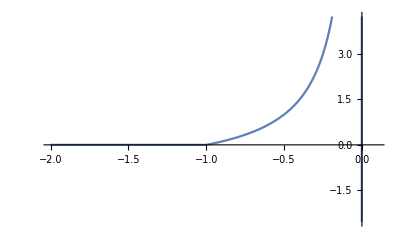

```mathematica
Plot[f[η],{η,-2,0.1}]
```

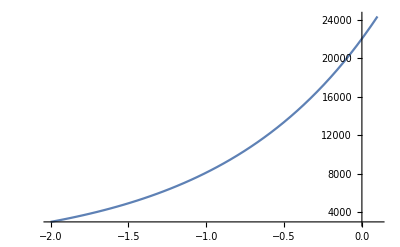

$Aborted

```mathematica
Plot[M[η],{η,-2,0.1}]
```

```mathematica
Sign[-3]
```

-1